### Statistics problem on hypothesis tests

#### Exercise 1

```mathematica
f[x_,"s"]:=3(x-1)^2;
f[x_,"b"]:=3 x^2;
```

```mathematica
Integrate[f[x,"s"],{x,0,1}]
Integrate[f[x,"b"],{x,0,1}]
```

1

1

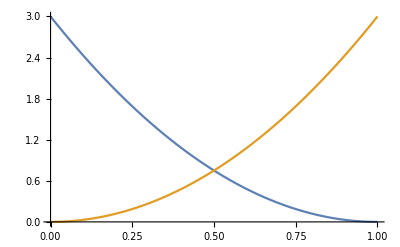

```mathematica
Plot[{f[x,"s"],f[x,"b"]},{x,0,1}]
```

(a) Efficiencies for selecting events with x<0.1

```mathematica
{ϵs,ϵb}=Integrate[f[x,#],{x,0,0.1}]&/@{"s","b"}
```

{0.271,0.001}

(b)

```mathematica
{πs,πb}={0.01,0.99};
TotalInTheRegion=πs ϵs+πb ϵb;
SignalInTheRegion=πs ϵs;
SignalInTheRegion/TotalInTheRegion
```

0.732432

(c)

```mathematica
f[0.05,"b"]/(f[0.05,"s"]+f[0.05,"b"])
```

0.00276243

I should have introduce π. (Bayes’ theorem P(b|x) P(x) = P(x|b) P(b), where P(b)=πb, P(x)=f[0.05, b]πb+f[0.05, s]πs, P(x|b)= f[0.05,b])

```mathematica
(f[0.05,"b"]πb)/(f[0.05,"s"]πs+f[0.05,"b"]πb)
```

0.215217

(d)

```mathematica
Integrate[f[x,"b"],{x,0,0.05}]
```

0.000125

p-value of a hypothesis is defined as the probability that the hypothesis gives more “extreme” events.
This immediately means that we have observed one very rare event.
Needless to say, as this is only one event, we should not give interpretation about the model.
p-value tells us about only the “bkg” hypothesis, and no implications on the “signal” hypothesis. Meanwhile, the value in (c) compares these two hypothesis.
Note that all the discussion is subjective.

(e) I assume that y is between 0 and 1.

```mathematica
f[x_,y_,"s"]:=6(x-1)^2 y
f[x_,y_,"b"]:=6 x^2(1-y)
Integrate[f[x,y,"s"],{x,0,1},{y,0,1}]
Integrate[f[x,y,"b"],{x,0,1},{y,0,1}]
```

1

1

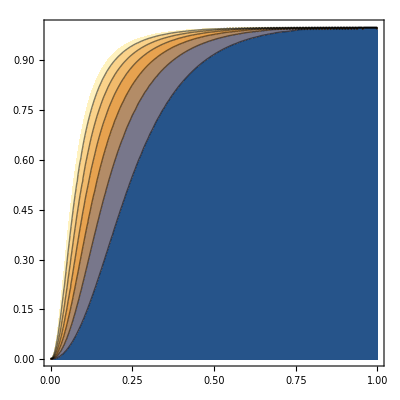

```mathematica
ContourPlot[(0.01f[x,y,"s"])/(0.01f[x,y,"s"]+0.99f[x,y,"b"]),{x,0,1},{y,0,1}]
```

From Neyman-Pearson lemma, which tells the most powerful (smallest β) detection for a given α,

```mathematica
f[x,y,"s"]/f[x,y,"b"]
```

The problem asks for a detection which gives highest signal purity (P(s) (1-β))/(P(b) α + P(s) (1-β)) for a given efficiency 1-β.
This is of course equivalent to the smallest α under a given β.

NP lemma guarantees that β based on this detection d_1, which can be writte as a function β(α;d_1), is no worse than that of others; ∀d,β(α;d_1)≤β(α;d) for given α.
Because β(α) is monotonically-decreasing, d_1 gives the smallest α under a given β.

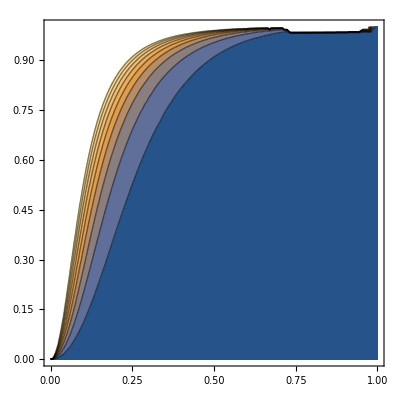

#### Exercise 2

```mathematica
1-Sum[(PDF@(PoissonDistribution[3.9]))[n],{n,0,16}]
√2 InverseErf[1-%]
```

8.08516×10^-7

4.9333